```mathematica
ClearAll["Global`*"]
```

## Forces

```mathematica
m=1.99;
g=9.80655;
v0=0;
x0=0;
θ=Pi/4;
v[t_]:=v0+g t Tan[θ];
x[t_]:=x0+v0 t+1/2 g t^2 Tan[θ];
```

```mathematica
x[1]
```

4.90328

```mathematica
v[3]
x[3]
```

29.4196

44.1295

```mathematica
a[t_]:=g Tan[θ]
v[t_]=Integrate[a[t], t]
x[t_]=Integrate[v[t],t]
```

9.80655 t

4.90328 t^2

```mathematica
(*For[i=0,i≤100,i++,
Print[i];
Print[v[i]];
Print[x[i]];
]*)
```

## Matrices & Angles

```mathematica
ClearAll[α,β,γ,m,g]
yaw = {{Cos[α], -Sin[α], 0},
	{Sin[α], Cos[α], 0},
	{0,0,1}};
pitch={{Cos[β],0,Sin[β]},
	{0,1,0},
	{-Sin[β],0,Cos[β]}};
roll={{1,0,0},
	{0,Cos[γ],-Sin[γ]},
	{0,Sin[γ],Cos[γ]}};
totalrotation=yaw.pitch.roll;
MatrixForm[totalrotation]
```

(Cos[α] Cos[β] | -Cos[γ] Sin[α]+Cos[α] Sin[β] Sin[γ] | Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]
Cos[β] Sin[α] | Cos[α] Cos[γ]+Sin[α] Sin[β] Sin[γ] | Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]
-Sin[β] | Cos[β] Sin[γ] | Cos[β] Cos[γ])

```mathematica
(*g=9.80655;
m=.056+1.518;
α=0;
β=0;
γ=π/6;*)
u={0,0,1};
fhat=totalrotation.u;
N[fhat];
MatrixForm[N[totalrotation]];
fz=fhat[[3]]
magf=(m*g)/fz
f=magf*fhat
```

Cos[β] Cos[γ]

g m Sec[β] Sec[γ]

{g m Sec[β] Sec[γ] (Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]),g m Sec[β] Sec[γ] (Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]),g m}

### Solve the ODE

```mathematica
(*f=ma*)
fg={0,0,-m*g}
fnet=f+fg
a=fnet/m
```

{0,0,-g m}

{g m Sec[β] Sec[γ] (Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]),g m Sec[β] Sec[γ] (Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]),0}

{g Sec[β] Sec[γ] (Cos[α] Cos[γ] Sin[β]+Sin[α] Sin[γ]),g Sec[β] Sec[γ] (Cos[γ] Sin[α] Sin[β]-Cos[α] Sin[γ]),0}

```mathematica
v=v0+a*dt;
x=x0+v*dt;
```

```mathematica
thing[α_,β_,γ_]:={g*m*Sec[β]*Sec[γ]*(Cos[α]*Cos[γ]*Sin[β]+Sin[α]*Sin[γ]),g*m*Sec[β]*Sec[γ]*(Cos[γ]*Sin[α]*Sin[β]-Cos[α]*Sin[γ]),0}/m
α=0;
β=0;
γ=π/6;
g=9.80655;
m=.056+1.518;
t0=0;
tf=1.0;
dt=0.05;
v0={0,0,0};
r0={0,0,0};
v=v0;
r=r0;
vt={{0,v0}};
rt={{0,r0}};
vyt={{0,v0[[2]]}};
yt={{0,r0[[2]]}};
For[t=dt,t<=tf,t=t+dt,
vn=v+thing[α,β,γ]*dt;
rn=r+v*dt;
v=vn;
r=rn;
AppendTo[vt,{t,v}];
AppendTo[rt,{t,r}];
AppendTo[vyt,{t,v[[2]]}];
AppendTo[yt,{t,r[[2]]}]]
```

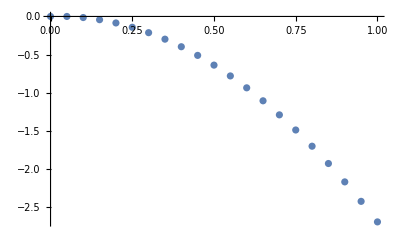

```mathematica
PaddedForm[TableForm[rt],{2,1}];
ListPlot[yt]
```

{0,-2.83091 s^2,0}

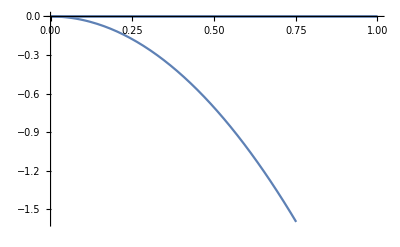

{0,-2.83091,0}

{1.,{0.,-2.68936,0.}}

```mathematica
integration[s_]=Integrate[thing[α,β,γ],s,s]
Plot[integration[s],{s,t0,tf}]
integration[tf]
rt[[-1]]
```